```mathematica
SetDirectory["C:\\Users\\User\\Desktop\\Experimentos MV2000\\Gabriela Flores\\Analisis GNRs\\FG163R"];
DatHeight=Import["DatosHeight.DAT","CSV"];
DatNSOM=Import["DatosNSOM.DAT","CSV"];
Length[DatHeight]
Length[DatNSOM]
NF=131072;
```

131072

131072

```mathematica
THeight=Table[0, {n,1,NF/2}];
RHeight=Table[0, {n,1,NF/2}];
TNSOM=Table[0, {n,1,NF/2}];
RNSOM=Table[0, {n,1,NF/2}];
```

```mathematica
For[i=1,i≤256,i++,
For[j=1,j≤256,j++,

THeight[[256(i-1)+j]]=DatHeight[[256((2i-1)-1)+j]];
RHeight[[256(i-1)+j]]=DatHeight[[256((2i-1))+j]];
TNSOM[[256(i-1)+j]]=DatNSOM[[256((2i-1)-1)+j]];
RNSOM[[256(i-1)+j]]=DatNSOM[[256((2i-1))+j]]
]
]
```

```mathematica
MTHeight=Table[0, {n,1,256},{m,1,256}];
MRHeight=Table[0, {n,1,256},{m,1,256}];
MTNSOM=Table[0, {n,1,256},{m,1,256}];
MRNSOM=Table[0, {n,1,256},{m,1,256}];

For[i=1,i≤256,i++,
For[j=1,j≤256,j++,

MTHeight[[256-(i-1),j]]=THeight[[256(i-1)+j,1]];
MRHeight[[256-(i-1),j]]=RHeight[[256(i-1)+(257-j),1]];
MTNSOM[[256-(i-1),j]]=TNSOM[[256(i-1)+j,1]];
MRNSOM[[256-(i-1),j]]=RNSOM[[256(i-1)+(257-j),1]]
]
]

Export["TAFM_FG163R.txt",MTHeight]
Export["RAFM_FG163R.txt",MRHeight]
Export["TNSOM_FG163R.txt",MTNSOM]
Export["RNSOM_FG163R.txt",MRNSOM]
```

TAFM_FG163R.txt

RAFM_FG163R.txt

TNSOM_FG163R.txt

RNSOM_FG163R.txt

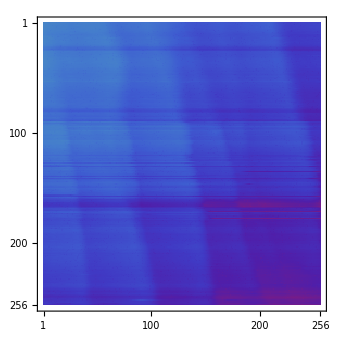
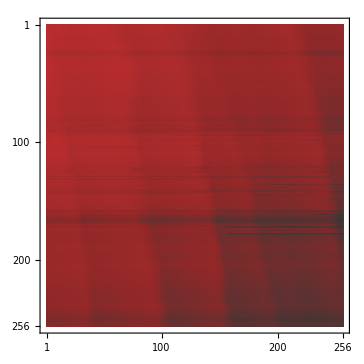

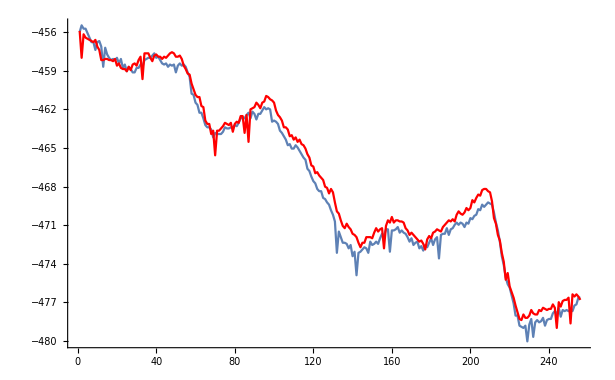

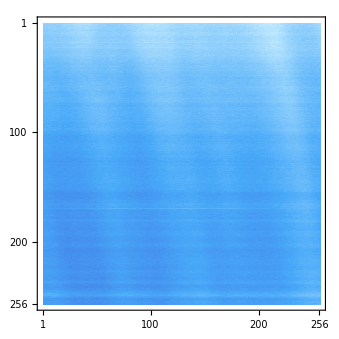
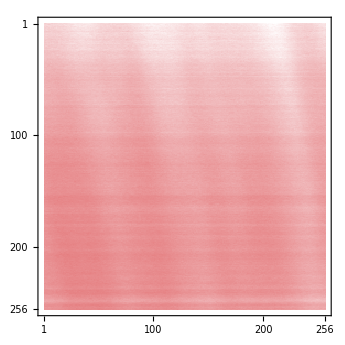

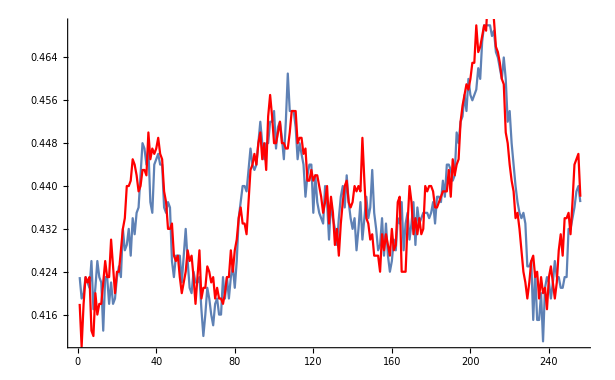

```mathematica
TraceHeight=MatrixPlot[MTHeight,ColorFunction->"Rainbow"];
RetraceHeight=MatrixPlot[MRHeight,ColorFunction->"CherryTones"];

TraceNSOM=MatrixPlot[MTNSOM,ColorFunction->"DeepSeaColors"];
RetraceNSOM=MatrixPlot[MRNSOM,ColorFunction->"CherryTones"];

Print[TraceHeight,RetraceHeight]
PerfTrace=ListLinePlot[MTHeight[[1]]];
PerfReTrace=ListLinePlot[MRHeight[[1]],PlotStyle->Red];
Show[PerfTrace,PerfReTrace]
Print[TraceNSOM,RetraceNSOM]
PerfTrace=ListLinePlot[MTNSOM[[1]]];
PerfReTrace=ListLinePlot[MRNSOM[[1]],PlotStyle->Red];
Show[PerfTrace,PerfReTrace]
```